## Constructive Effect of Interference

Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../../neupackage/mma/neutrino.wl"]
```

```mathematica
Get["../../../neupackage/mma/neumat.wl"]
```

```mathematica
colorpalette5={RGBColor[172,151,62],
RGBColor[129,118,204],
RGBColor[91,169,102],
RGBColor[199,90,147],
RGBColor[204,95,67]}
```

{RGBColor[172,151,62],RGBColor[129,118,204],RGBColor[91,169,102],RGBColor[199,90,147],RGBColor[204,95,67]}

```mathematica
markers=Graphics`PlotMarkers[]
```

{{●,8.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

Rabi Oscillation

```mathematica
ampRabi[a_,k_,omegam_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2);
```

```mathematica
probRabi[a_,k_,omegam_,x_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2)Sin[(√(Abs[a]^2+(k-omegam)^2))/2 x]^2;
```

```mathematica
probRabi[a_,k_,omegam_,x_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2)Sin[(√(Abs[a]^2+(k-omegam)^2))/2 x]^2;
```

Parameters

```mathematica
endpoint=140000;
endpoint2=400000;
endpoint3=500;
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
energy20=20;(*Energy in units of MeV*)
?OmegaVacuum
omegaV=OmegaVacuum[energy10,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093]/2

energy20=20;(*Energy in units of MeV*)

fraction=0.5(*0.99*)
lambdaN=fraction*Cos[2thetaV]omegaV (*MeV*)

thetamVN=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi];

omegaV=OmegaVacuum[energy20,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)
lambdaN=0.5*Cos[2thetaV]omegaV (*MeV*)
omegaM=OmegaMatter2[lambdaN,thetaV,omegaV](*MeV*)
thetamV=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi]

datafracStashFullTicks:=Table[{x,ScientificForm[MeVInverse2km[x/omegaM],2]},{x,0,endpoint}];
(*datafracStashTicks[i_]:=Take[datafracStashFullTicks[i],{1,Length@datafracStashFullTicks[i],Floor[(Length@datafracStashFullTicks[i])/5]}];*)
datafracStashTicks:=Table[{x,ScientificForm[MeVInverse2km[x/omegaM],2]},{x,0,endpoint,Floor[endpoint/5]}];
```

Takes [energy_,deltam2_] as parameters and calculates ω_v. Should becareful about units.

1.3×10^-16

0.154948

0.5

6.19038×10^-17

6.5×10^-17

3.09519×10^-17

3.67552×10^-17

0.198931

Functions

```mathematica
solNumRabi[kList_,aList_,endpointModule_]:=Module[{sysM,lenM},

lenM=Length@kList;

(*sysM=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(Total[Table[aList[[n]]Cos[kList[[n]]x],{n,1,lenM}]])PauliMatrix[1]/2(*+(Total[Table[aList[[n]]Sin[kList[[n]]x],{n,1,lenM}]])PauliMatrix[2]/2*)).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};
*)
sysM=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(Total[Table[aList[[n]]Cos[kList[[n]]x],{n,1,lenM}]])PauliMatrix[1]/2+(Total[Table[aList[[n]]Sin[kList[[n]]x],{n,1,lenM}]])PauliMatrix[2]/2(*+(Total[Table[aList[[n]]Sin[kList[[n]]x],{n,1,lenM}]])PauliMatrix[2]/2*)).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

NDSolve[sysM,{psi1,psi2},{x,0,endpointModule}]
]
```

```mathematica
solutionLists[solutions_,endpointModule_,stepsize_]:=Module[{lenM},
lenM=Length@solutions;

Table[
Table[{x,(Abs[psi2[x]]^2)/.solutions[[i,1]]},{x,0,endpointModule,stepsize}]
,{i,1,lenM}]
]

solutionNeutrinoLists[solutions_,endpointModule_,stepsize_]:=Module[{lenM},
lenM=Length@solutions;

Table[
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solutions[[i,1]]},{x,0,endpointModule,stepsize}]
,{i,1,lenM}]
]
```

```mathematica
gridlinesFull[omegam_,kList_,aList_]:=1/(1+rDFull[omegam,kList[[1]],kList[[2]],aList[[1]],aList[[2]]]^2)
gridlines[omegam_,kList_,aList_]:=1/(1+rD[omegam,kList[[1]],kList[[2]],aList[[1]],aList[[2]]]^2)
qvaluesFull[omegam_,kList_,aList_]:=rDFull[omegam,kList[[1]],kList[[2]],aList[[1]],aList[[2]]]
qvalues[omegam_,kList_,aList_]:=rD[omegam,kList[[1]],kList[[2]],aList[[1]],aList[[2]]]
```

## Destruction Criteria

```mathematica
a2FromQ[a_,q_]:=√(2a q)
```

We can define the non-approximate formula for relative detuning

```mathematica
rDFull[omegam_,k1_,k2_,a1_,a2_]:=Abs[((omegam-k2)√(1+a2^2/(omegam-k2)^2)-(k1-k2))/a1]
```

```mathematica
rD[omegam_,k1_,k2_,a1_,a2_]:=Abs[((omegam-k1)+1/2 a2^2/(omegam-k2))/a1]
```

Identifying the constructive parameters

```mathematica
conParamk2[a2_,k1_]:=a2^2/(2*(1-k1))+1
```

```mathematica
Plot3D[Abs@(conParamk2[a2,k1]-1)/a2,{a2,0.01,1.1},{k1,0.01,1.99},PlotLegends->Automatic,AxesLabel->Automatic]
```

-Graphics3D-

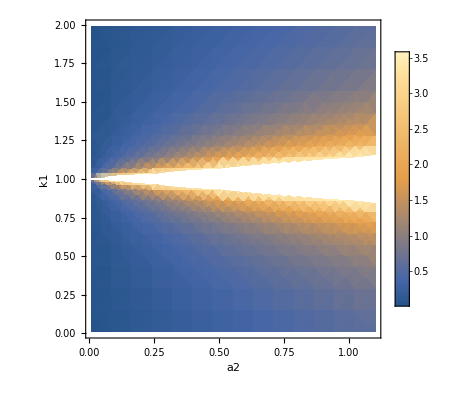

```mathematica
DensityPlot[Abs@(conParamk2[a2,k1]-1)/a2,{a2,0.01,1.1},{k1,0.01,1.99},PlotLegends->Automatic,FrameLabel->Automatic]
```

```mathematica
conParamk2[0.4,0.95]
```

2.6

Numerical Solutions

```mathematica
kList1={0.95,2.6};
aList1={0.025,0.4};

kList2={0.95,0};
aList2={0.025,0};

kList3={2.6,0};
aList3={0.4,0};

kList={kList1,kList2,kList3};
aList={aList1,aList2,aList3};


solNumRabiAll=Table[
solNumRabi[kList[[i]],aList[[i]],endpoint3],
{i,1,Length@kList}]
sols=solutionLists[solNumRabiAll,endpoint3,0.01];


gridlinesListFull=Table[gridlinesFull[1,kList[[i]],aList[[i]]],{i,1,Length@kList}];
gridlinesList=Table[gridlines[1,kList[[i]],aList[[i]]],{i,1,Length@kList}];

qvaluesFullList=Table[qvaluesFull[1,kList[[i]],aList[[i]]],{i,1,Length@kList}]
qvaluesList=Table[qvalues[1,kList[[i]],aList[[i]]],{i,1,Length@kList}]

plotleg=Table["k="<>ToString[N@kList[[i]]]<>";a="<>ToString[N@aList[[i]]]<>";",{i,1,Length@kList}]
```

{{{psi1→InterpolatingFunction[…],psi2→InterpolatingFunction[…]}},{{psi1→InterpolatingFunction[…],psi2→InterpolatingFunction[…]}},{{psi1→InterpolatingFunction[…],psi2→InterpolatingFunction[…]}}}

{0.03031,2.,4.}

{1.38778×10^-15,2.,4.}

{k={0.95, 2.6};a={0.025, 0.4};,k={0.95, 0.};a={0.025, 0.};,k={2.6, 0.};a={0.4, 0.};}

```mathematica
predictions=Table[{t,1/(1+rD[1,kList1[[1]],kList1[[2]],aList1[[1]],aList1[[2]]]^2)*Sin[t*aList1[[1]]√(1+rD[1,kList1[[1]],kList1[[2]],aList1[[1]],aList1[[2]]]^2)/2]^2},{t,0,endpoint3,0.1}]
```

{{0.,0.},{0.1,1.5625×10^-6},{0.2,6.24999×10^-6},{0.3,0.0000140624},{0.4,0.0000249998},4992,{499.7,0.0013636},{499.8,0.0012729},{499.9,0.00118532},{500.,0.00110086}}
 |  |  |  |

```mathematica
idxEnd=3;
ListPlot[
Join[sols[[1;;idxEnd]],{predictions}]
,Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks}},GridLines->{None, gridlinesList[[1;;idxEnd]]},PlotRange->{(*{0,2 10^5}*){0,endpoint3},Automatic},PlotStyle->{Black,Red,Blue,Magenta,Cyan,Yellow,Green},PlotLegends->Placed[plotleg[[1;;idxEnd]],{Center,Below}]]
```

-Graphics-

```mathematica
Export["constructive1-predictions.csv",predictions]
```

constructive1-predictions.csv